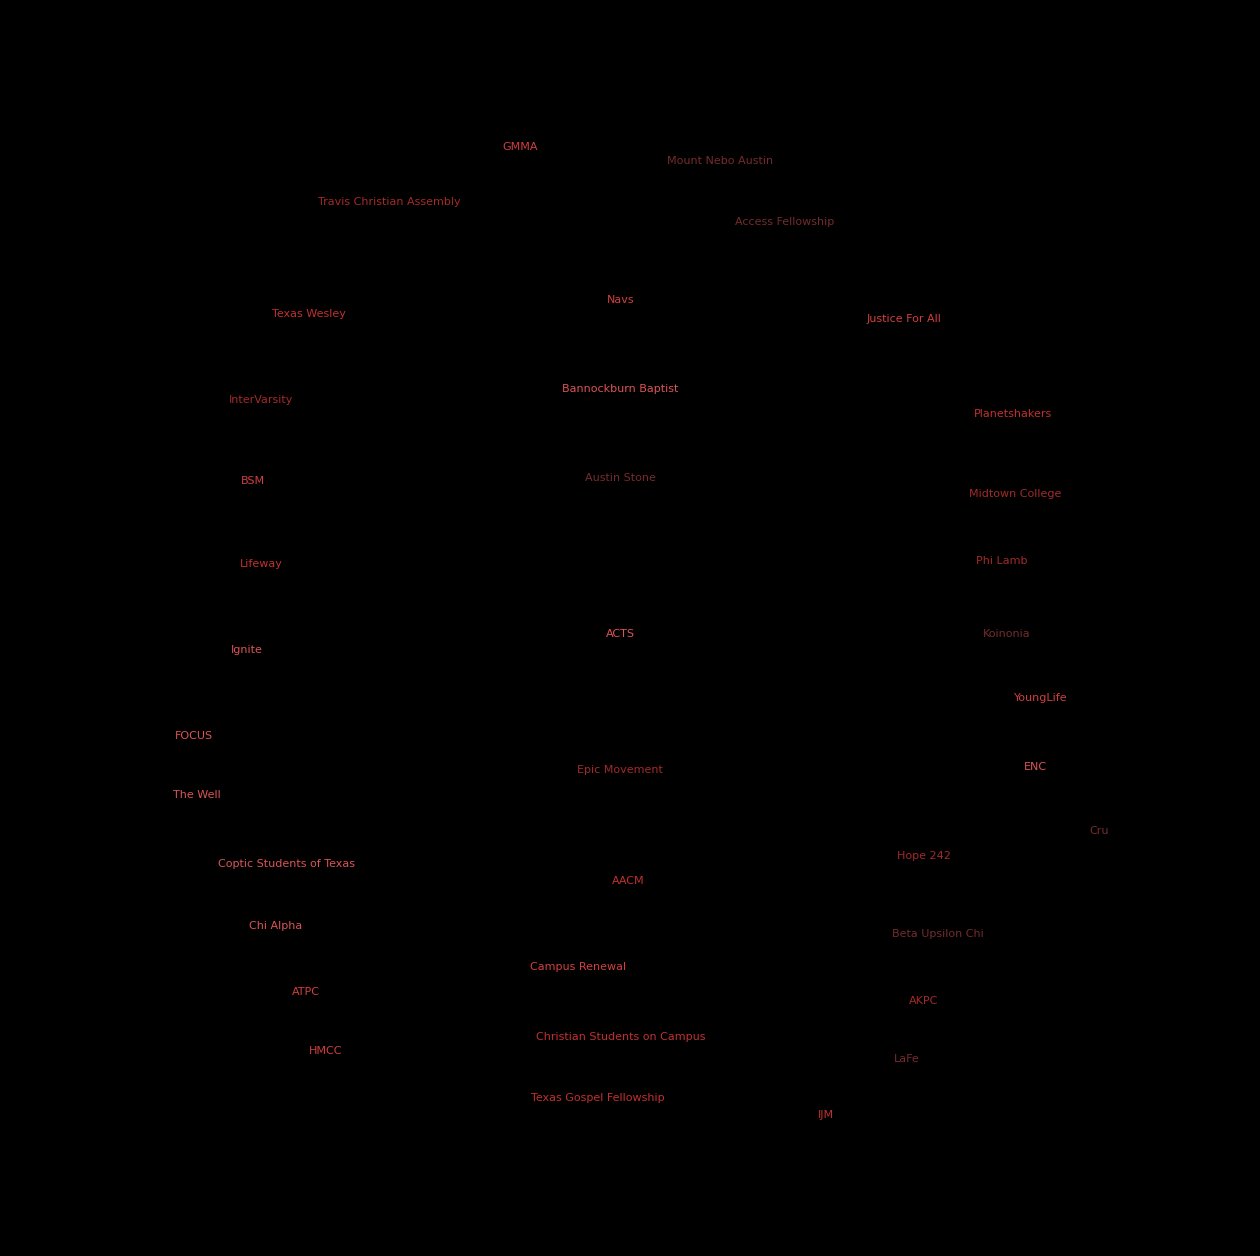

/Users/Evan/GitProjects/campusmap/RezWeekCal/wordcloud.png

Volunteer_Status.jpg

```mathematica
wc=WordCloud[
{48->"AACM",99->"ACTS",5->"AKPC",4->"ATPC",11->"Access Fellowship",40->"Austin Stone",24->"BSM",16->"Bannockburn Baptist",5->"Beta Upsilon Chi",14->"Campus Renewal",5->"Chi Alpha",4->"Christian Students on Campus",1->"Coptic Students of Texas",3->"Cru",10->"ENC",43->"Epic Movement",3->"FOCUS",3->"GMMA",1->"HMCC",17->"Hope 242",1->"IJM",25->"Ignite",4->"InterVarsity",8->"Justice For All",17->"Koinonia",2->"LaFe",22->"Lifeway",1->"Midtown College",1->"Mount Nebo Austin",51->"Navs",13->"Phi Lamb",6->"Planetshakers",3->"Texas Gospel Fellowship",14->"Texas Wesley",1->"The Well",3->"Travis Christian Assembly",1->"YoungLife"},
Background->Transparent,ColorFunction->Reverse[Table[ColorData["CherryTones"][i],{i,0.1,.5,0.1}]],
WordSpacings->5,
ImageSize->1260]
Export["/Users/Evan/GitProjects/campusmap/RezWeekCal/wordcloud.png",wc,"PNG"]
SetDirectory["/Users/Evan/GitProjects/campusmap/RezWeekCal"];
Export["Volunteer_Status.jpg",ImageAssemble[{Import/@FileNames["*_cal.png"]}], ImageSize->1920]
```

```mathematica
CloudDeploy[FormFunction[{"profile"->"Image"},Block[{filter,img,size},

img = #profile;
filter=-Graphics-;
(* Crop the profile to the middle square *)
size=Min[ImageDimensions[img]];
img=ImageCrop[img,{size,size}];

(* Using the min ensures highest resolution *)
size=Min[size,ImageDimensions[filter]];

(* Scale images to the same size *)
img=ColorConvert[ImageResize[img,size],"Grayscale"];
filter=ImageResize[filter,size];

ImageAdjust[Blend[{img,filter}],{.1,.1}]]&,"PNG"],Permissions->"Public"]
```